## Initialization

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
Directory[]
```

/Users/npadmana/myWork/np_sandbox/CLASS

## Power Spectrum conventions

Check to see if we have the correct power spectrum conventions for the primordial power spectrum. Well, I don’t quite understand the convention used as yet, I determined it for now by experimentation????

```mathematica
(* Read in the power spectrum and plot it -- do this at z=0 *)
```

```mathematica
pk0 = Import["output/synchronous_z1_pk.dat","Table"]//DeleteCases[#, {"#",___}] & ;
```

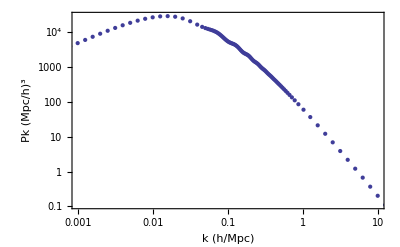

```mathematica
ListLogLogPlot[pk0, PlotRange->{{0.001, 10}, All}, Frame->True, FrameLabel-> {"k (h/Mpc)", "Pk (Mpc/h)^3"}]
```

```mathematica
(* Now read in the transfer functions *)
```

In synchronous gauge, the CDM has no peculiar velocities, so we only need to pull out the baryon velocity transfer function.

```mathematica
(* col 1 is k, col 6 is transfer function for density, col 8 is baryon v transfer fn *)
```

```mathematica
transfer0 = Import["output/synchronous_z1_tk.dat", "Table"]//DeleteCases[#, {"#", ___}] & // Part[#, All, {1,6, 8}] & ;
```

```mathematica
(* Now let us see if we can match the two power spectra, start by defining the primordial P(k) *)

Clear[pkPrim];
pkPrim[k_] := With[{ns=0.966, As=2.4*^-9, kpivot=0.002}, As (k/kpivot)^(ns-1)];
```

```mathematica
(* Now scan through the transfer function list and calculate pk *)
```

```mathematica
Clear[pkcalc];pkcalc[kh_, tcdm_, vbary_]:= With[{h=0.703}, {kh, 2 π^2*kh*tcdm^2*pkPrim[kh*h]/kh^4}];
```

```mathematica
pk0test = pkcalc@@@transfer0;
```

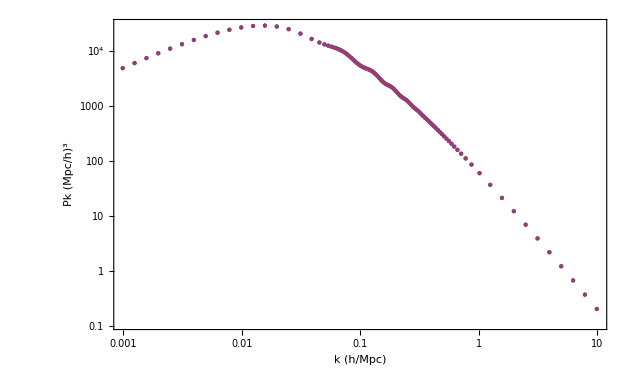

```mathematica
ListLogLogPlot[{pk0, pk0test}, PlotRange->{{0.001, 10}, All}, Frame->True, FrameLabel-> {"k (h/Mpc)", "Pk (Mpc/h)^3"}]
```

## Velocity Power Spectrum at z=15

```mathematica
(* As a test that we are mostly doing all of this correctly, let's try to compute the power spectrum plotted in Dalal et al, 2010, Fig. 1 (Left) *)
(* Start by reading in the redshift 15 transfer fn.*)
```

```mathematica
transfer1 = Import["output/synchronous_z2_tk.dat", "Table"]//DeleteCases[#, {"#", ___}] & // Part[#, All, {1,6, 8}] & ;
```

```mathematica
(* Define the power spectrum -- note this is Δ^2 *)
```

```mathematica
Clear[vpkcalc]; 
vpkcalc[kh_, tcdm_, vbary_]:= With[{h=0.703}, {kh, (3*^5)^2 vbary^2*pkPrim[kh*h]/(kh^2 h^2)}];
```

```mathematica
vpk1test = vpkcalc@@@ transfer1;
```

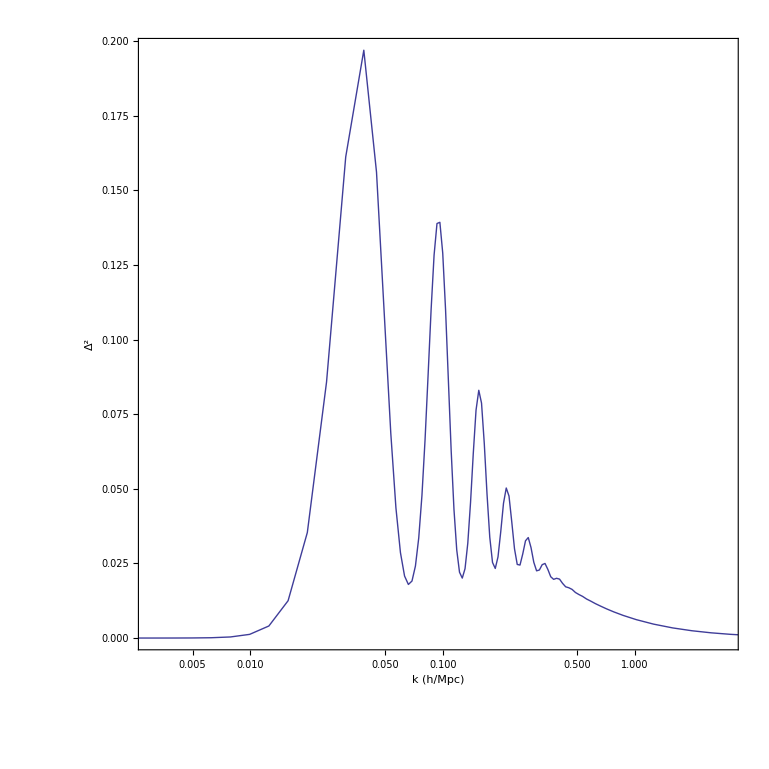

```mathematica
ListLogLinearPlot[vpk1test, PlotRange->{{0.003, 3}, All}, Frame->True, FrameLabel-> {"k (h/Mpc)", "Δ^2"}, Joined->True, AspectRatio->1]
```

The above matches the power spectrum in Dalal et al. Use it for now, ignoring subtleties about normalization????. Do this at z=0 as well for now.

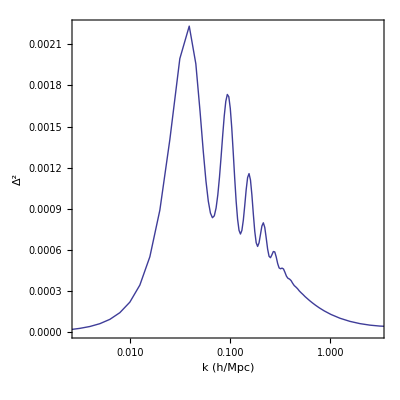

```mathematica
vpk0test = vpkcalc@@@ transfer0;
ListLogLinearPlot[vpk0test, PlotRange->{{0.003, 3}, All}, Frame->True, FrameLabel-> {"k (h/Mpc)", "Δ^2"}, Joined->True, AspectRatio->1]
```

Now let us interpolate this function

```mathematica
vpk1int = Interpolation[vpk1test]
```

InterpolatingFunction[{{1.97552×10^-7,12.4775}},<>]

We should be careful here that h’s don’t come back to bite us, we will try to work that soon.?????

```mathematica
sigma1 = Sqrt[NIntegrate[vpk1int[k]/k, {k, 1.*^-5, 10}]/3]
```

0.286319

## What does the velocity transfer function look like?

Extract the velocity transfer function

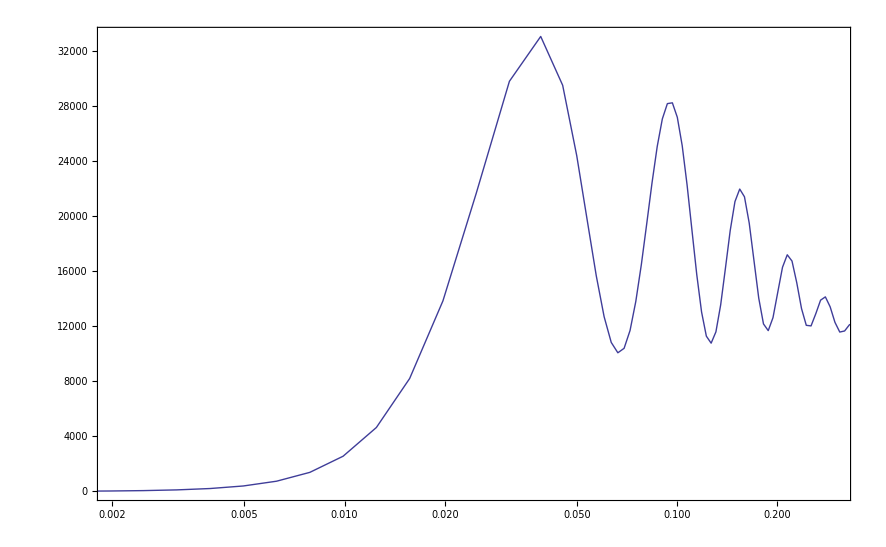

```mathematica
vT1 = {#1, 3*^5 *#3/(-#1*0.703*sigma1)}& @@@ transfer1;
ListLogLinearPlot[vT1, PlotRange->{{0.002, 0.3}, All}, Frame->True, Joined->True]
```

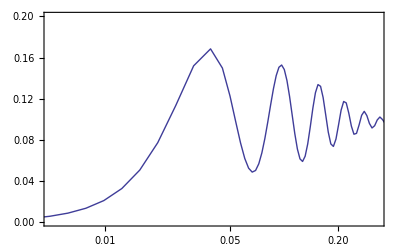

```mathematica
(* Compute the G(u) term as well *)
g1 = {#1, 3*^5*#3/(2 π^2*0.703 * #1*sigma1 *#2)}& @@@ transfer1;
g1k = {#1, #1*#2} & @@@ g1;
ListLogLinearPlot[g1k,  PlotRange->{{0.005, 0.33}, {0,0.2}}, Frame->True, Joined->True]
```

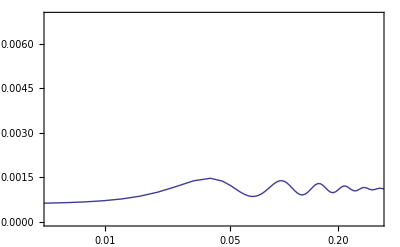

```mathematica
(* Compute the G(u) term as well *)
g0 = {#1, 3*^5*#3/(2 π^2*0.703 * #1*sigma1 *#2)}& @@@ transfer0;
g0k = {#1, #1*#2} & @@@ g0;
ListLogLinearPlot[g0k,  PlotRange->{{0.005, 0.33},All}, Frame->True, Joined->True]
```

```mathematica
Export["Gru.txt", g1, "Table"]
```

Gru.txt